```mathematica
Expand[(x-1)^2]
```

1-2 x+x^2

```mathematica
%
```

1-2 x+x^2

```mathematica
Factor[%]
```

(-1+x)^2

```mathematica
Cancel[(x^2-1)/(x-1)]
```

1+x

```mathematica
Simplify[1-2x+x^2]
```

(-1+x)^2

```mathematica
FullSimplify[1-2x+x^2]
```

(-1+x)^2

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
Simplify[Sqrt[x^2]]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x>0]
```

x

```mathematica
Refine[Sqrt[x^2],x>0]
```

x

```mathematica
Refine[Sqrt[x^2+2x y+y^2],x+y>0]
```

√(x^2+2 x y+y^2)

```mathematica
FullSimplify[Sqrt[x^2+2x*y+y^2],x+y>0]
```

x+y

```mathematica
(*Complex*)
I^2
```

-1

```mathematica
ⅈ^2
```

-1

```mathematica
complex=2+3ⅈ
```

2+3 ⅈ

```mathematica
Re[complex]
```

2

```mathematica
Im[complex]
```

3

```mathematica
Abs[complex]
```

√13

```mathematica
Conjugate[complex]
```

2-3 ⅈ

```mathematica
(*EndComplex*)

f[x_]:=2(x-4)^2+1
```

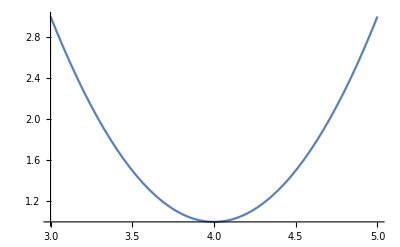

```mathematica
Plot[f[x],{x,3,5}]
```

```mathematica
p[x_]:=3x+8x^2
```

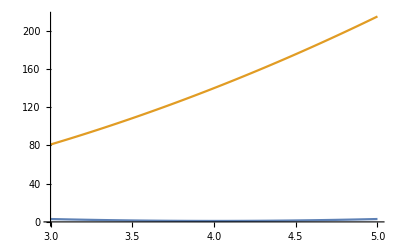

```mathematica
Plot[{f[x],p[x]},{x,3,5}]
```

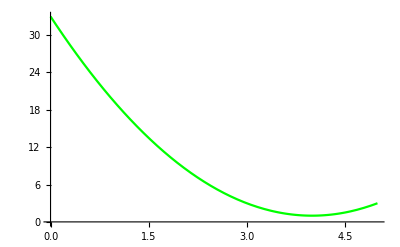

```mathematica
Plot[f[x],{x,0,5},PlotStyle->Green]
```

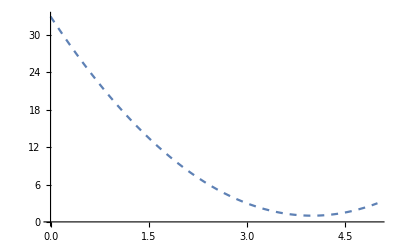

```mathematica
Plot[f[x],{x,0,5},PlotStyle->Dashed]
```

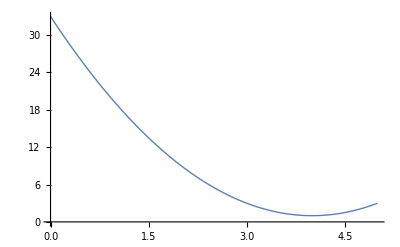

```mathematica
Plot[f[x],{x,0,5},PlotStyle->Thick]
```

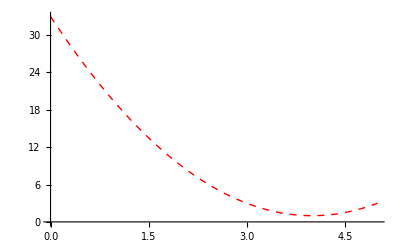

```mathematica
(*Plot[f[x],{x,0,5},PlotStyle->Thickness[0]]*)
plotl=Plot[f[x],{x,0,5},PlotStyle->{Dashed,Red,Thick}]
```

```mathematica
data=Table[{k,k^2},{k,0,10}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

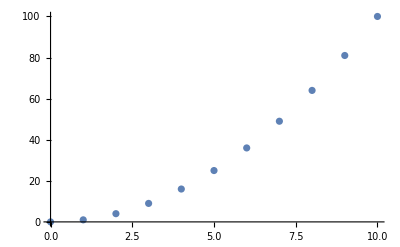

```mathematica
ListPlot[data]
```

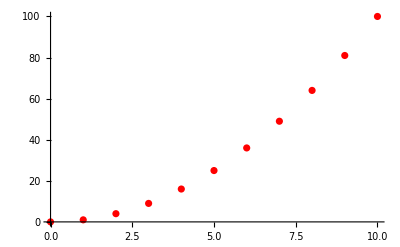

```mathematica
lp=ListPlot[data,PlotStyle->Red]
```

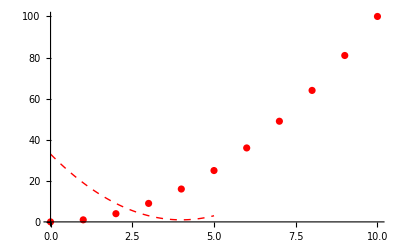

```mathematica
Show[ListPlot[data,PlotStyle->Red],Plot[f[x],{x,0,5},PlotStyle->{Dashed,Red,Thick}]]
```

```mathematica
Show[lp,plotl]
```

-Graphics-

```mathematica
(*Task1*)
Simplify[(x+y)/2≥√(x*y),{x≥0,y≥0}]
```

True

```mathematica
(*Task2*)

p[x_]:=2x^5+5x^4-8x^3-14x^2+6x+9
```

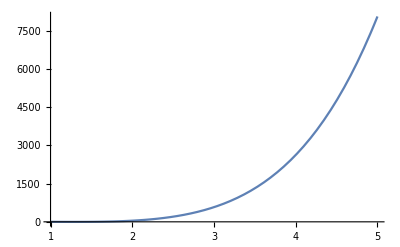

```mathematica
Plot[p[x],{x,1,5}]
```

```mathematica
Factor[p[x]]
```

(-1+x) (1+x)^2 (3+x) (-3+2 x)

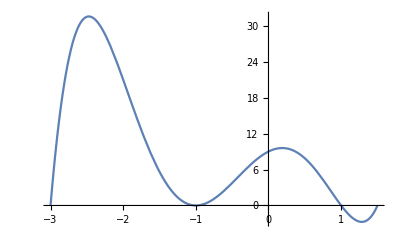

```mathematica
Plot[p[x],{x,-3.0,1.5}]
```

```mathematica
Plot[p[x],{x,-3.0,3.0}]
```

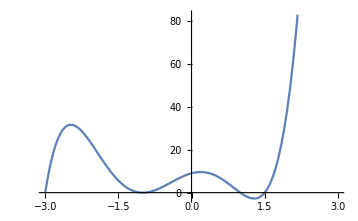
```mathematica
-Graphics-
(*Task3a*)
```

```mathematica
complex[z_Complex]:=√((Re[z])^2+(Im[z])^2)
```

```mathematica
complex[2ⅈ+5]
```

√29

```mathematica
complex[4ⅈ+4]
```

4 √2

```mathematica
√((Re[2ⅈ+5])^2+(Im[2ⅈ+5])^2)
```

√29

```mathematica
√((Re[4ⅈ+4])^2+(Im[4ⅈ+4])^2)
```

4 √2

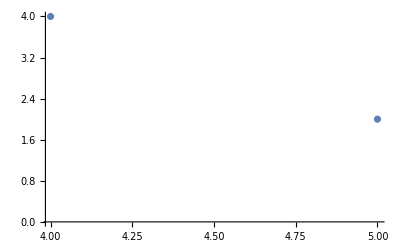

```mathematica
ListPlot[{{5.0,2.0},{4.0,4.0}}]
```

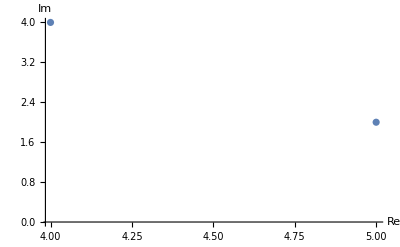

```mathematica
ListPlot[{{5.0,2.0},{4.0,4.0}},AxesLabel->{Re,Im}]
```

```mathematica
(*From 19.11.19 *)
Simplify[1-2x+x^2]
```

(-1+x)^2

```mathematica
FullSimplify[1-2x+x^2]
```

(-1+x)^2

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
Expand[(1-x)^2]
```

1-2 x+x^2

```mathematica
Factor[%]
```

(-1+x)^2

```mathematica
Simplify[Sqrt[x^2]]
```

√(x^2)

```mathematica
Simplify[Sqrt[x^2],x>0]
```

x

```mathematica
Refine[Sqrt[x^2],x>0]
```

x

```mathematica
Refine[Sqrt[x^2],x<0]
```

-x

```mathematica
I^2
```

-1

```mathematica
ⅈ^2
```

-1

```mathematica
c=2ⅈ+5
```

5+2 ⅈ

```mathematica
Re[c]
```

5

```mathematica
Im[c]
```

2

```mathematica
Abs[c]
```

√29

```mathematica
Conjugate[c]
```

5-2 ⅈ

```mathematica
Mod[17,4]
```

1

```mathematica
Divisible[17,4]
```

False

```mathematica
f[x_]:=x^2
```

```mathematica
f1[list1_,list2_]:=
(
list3=list2-list1;
Print[list3];
ListPlot[list3]
)
```

```mathematica
l1={1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
l2={3,1,4,7,8}
```

{3,1,4,7,8}

{2,-1,1,3,3}

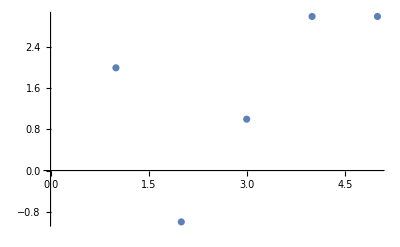

```mathematica
f1[l1,l2]
```

```mathematica
x={1.6,2.7,4.7,5,6};
```

```mathematica
f[x]
```

{2.56,7.29,22.09,25,36}

```mathematica
y=f[x]
```

{2.56,7.29,22.09,25,36}

```mathematica
{x,y}
```

{{1.6,2.7,4.7,5,6},{2.56,7.29,22.09,25,36}}

```mathematica
{x,y}//MatrixForm
```

(1.6 | 2.7 | 4.7 | 5 | 6
2.56 | 7.29 | 22.09 | 25 | 36)

```mathematica
Transpose[{x,y}]
```

{{1.6,2.56},{2.7,7.29},{4.7,22.09},{5,25},{6,36}}

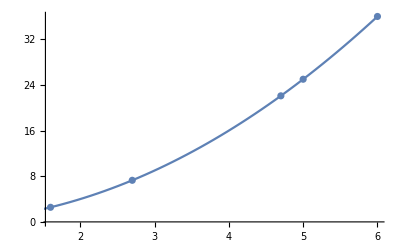

```mathematica
Show[ListPlot[Transpose[{x,y}]],Plot[z^2,{z,1.5,6}]]
```

```mathematica
g[x_]:=100Cos[x]+E^x
```

```mathematica
Clear[x]
```

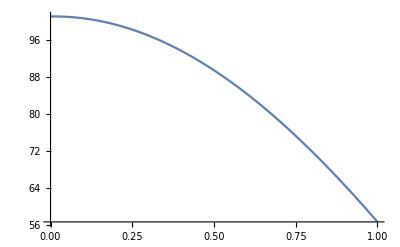

```mathematica
Plot[g[x],{x,0,1}]
```

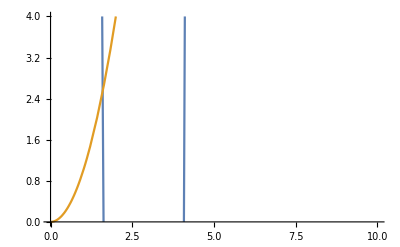

```mathematica
Plot[{g[x],f[x]},{x,0,10},PlotRange->{0,4}]
```

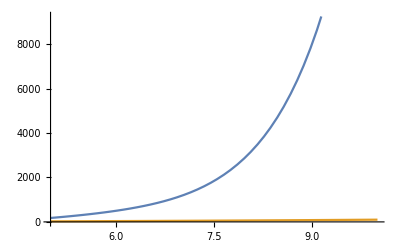

```mathematica
Plot[{g[x],f[x]},{x,5,10}]
```

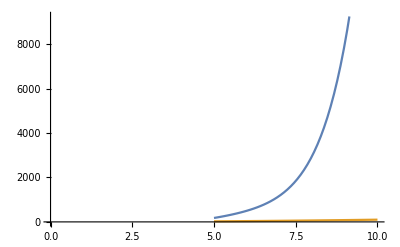

```mathematica
Plot[{g[x],f[x]},{x,5,10},AxesOrigin->{0,0}]
```

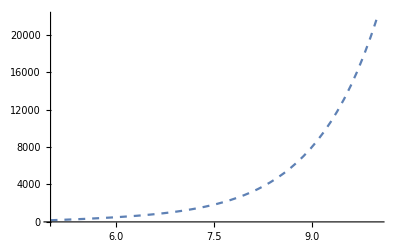

```mathematica
Plot[g[x],{x,5,10},PlotStyle->Dashed]
```

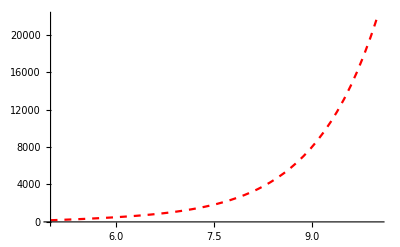

```mathematica
Plot[g[x],{x,5,10},PlotStyle->{Dashed,Red}]
```

```mathematica
(*Task0*)
f[a_Real,b_Real,c_Real]:=(
x1=(-b+Sqrt[b^2-4 a c])/(2 a);
x2=(-b-Sqrt[b^2-4 a c])/(2 a);
{x1,x2});
```

```mathematica
f[2.0,5.0,3.0]
```

{-1.,-1.5}

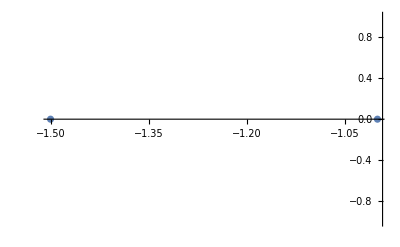

```mathematica
ListPlot[{{-1.0,0.0},{-1.5,0.0}}]
```

```mathematica
(*Task3a*)
complex[z_Complex]:=√((Re[z])^2+(Im[z])^2)
```

```mathematica
complex[2ⅈ+5]
```

√29

```mathematica
complex[4ⅈ+4]
```

4 √2

```mathematica
√((Re[2ⅈ+5])^2+(Im[2ⅈ+5])^2)
```

√29

```mathematica
√((Re[4ⅈ+4])^2+(Im[4ⅈ+4])^2)
```

4 √2

```mathematica
(*Task3b*)
```

```mathematica
ListPlot[{{5.0,2.0},{4.0,4.0}}]
```

-Graphics-

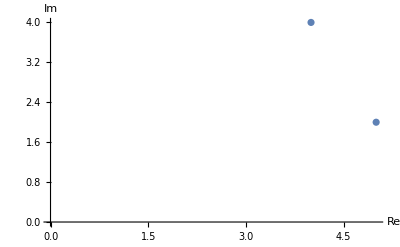

```mathematica
g1=ListPlot[{{5.0,2.0},{4.0,4.0}},AxesLabel->{Re,Im},AxesOrigin->{0.0,0.0}]
```

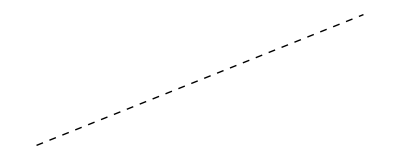

```mathematica
g2=Graphics[{Dashed,Line[{{0.0,0.0},{5.0,2.0}}]}]
```

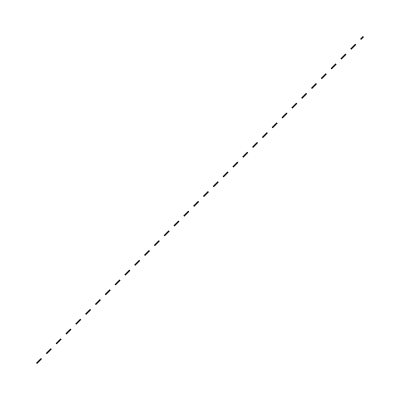

```mathematica
g3=Graphics[{Dashed,Line[{{0.0,0.0},{4.0,4.0}}]}]
```

```mathematica
Show[g1,g2,g3]
```

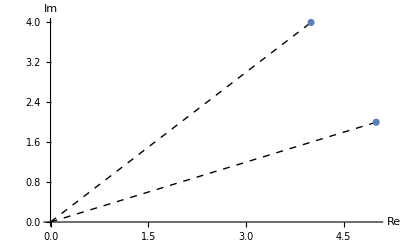

```mathematica
complexNumberVisualise[z_]:=(
Show[ListPlot[{{Re[z],Im[z]}},PlotMarkers->Automatic,AxesLabel->{Re,Im}],
Plot[Im[z]/Re[z]x,{x,0,Re[z]},PlotStyle->Dashed],
PlotRange->All,AxesOrigin->{0,0}]
)
```

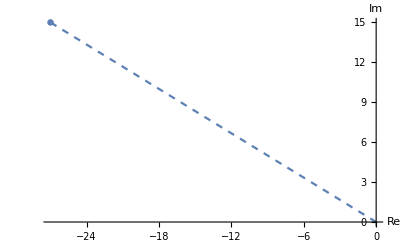

```mathematica
complexNumberVisualise[15 ⅈ-27]
```

```mathematica
(*Task4*)
```

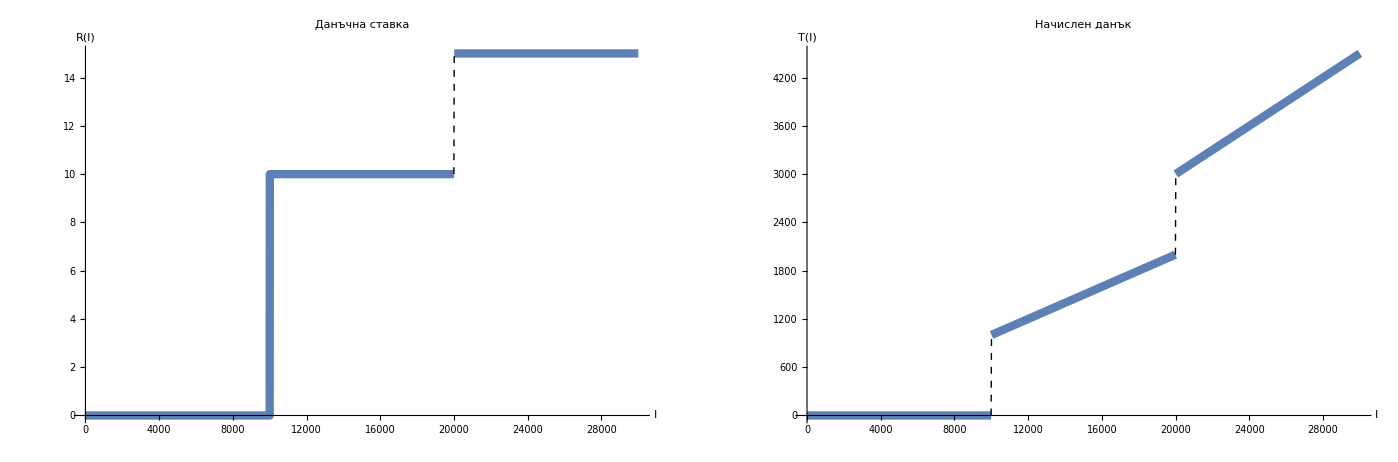

```mathematica
R[x_]:=Piecewise[{{0, x≤10000}, {10, 10000<x≤20000}, {15, True}}]
GraphicsRow[{Plot[R[x],{x,0,30000},Exclusions->{10000,20000},ExclusionsStyle->Dashed,PlotStyle->Thickness[0.015],PlotLabel->"Данъчна ставка", AxesLabel->{"I","R(I)"}],
Plot[R[x]/100 x,{x,0,30000},Exclusions->{10000,20000},ExclusionsStyle->Dashed,PlotStyle->Thickness[0.015],PlotLabel->"Начислен данък", AxesLabel->{"I","T(I)"}]}]
```